```mathematica
five=Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&];Length[five]
```

64

```mathematica
fiveSorted=Sort[five,Length[ListofVars[allGraphs4[#1,"colofour"]]]>Length[ListofVars[allGraphs4[#2,"colofour"]]]&];
```

```mathematica
fiveEdges=Block[{i,j, main,mainVars, sub,subVars,result={}},
Monitor[
For[i=1,i≤Length[fiveSorted],i++,
main=fiveSorted[[i]];
mainVars=ListofVars[allGraphs4[main,"colofour"]];
For[j=i+1,j≤Length[fiveSorted],j++,
sub=fiveSorted[[j]];
subVars=ListofVars[allGraphs4[sub,"colofour"]];
If[SubSetQ[mainVars,subVars],
AppendTo[result,main->sub]
]
]
],
{i,j,Length[result]}
];
result
];
```

```mathematica
gCleaned=Block[{g=Graph[fiveEdges],vertices,paths,cleaned=0},
vertices=Sort[VertexList[g]];
Monitor[
Table[
paths=FindPath[g,e[[1]],e[[2]],{2,100}];
If[Length[paths]≠0,
g=EdgeDelete[g,e];
cleaned++
]
,{e,Sort[fiveEdges]}
],
{e,cleaned}
];
Print[cleaned];
g
];
```

473

```mathematica
EdgeCount[gCleaned]
```

192

```mathematica
Length[fiveEdges]
```

665

```mathematica
FindPath[Graph[fiveEdges],0,81]
```

{{0,81}}

```mathematica
FindPath[gCleaned,0,4,{0,1}]
```

{}

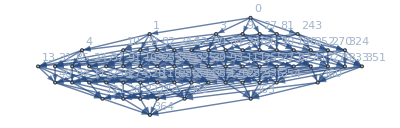

```mathematica
Graph[gCleaned,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Table[k->Labeled[allGraphs4[k,"graph"],Style[k,Blue]],{k,fiveSorted}]]
```